Carbapenem Resistance Model:

Objective: Whereas a clear correlation exists between consumption of antibiotics and the evolution of resistance in microbial communities, the effect of reduction of usage is less clear. To project the future frequency of carbapenem resistance, based on yearly surveillance data and consumption data. A population genetic model was adapted to retrospectively estimate the relationship between evolutionary fitness of carbapenem resistance and carbapenem consumption.

Derivation: We fit the historical selection to consumption via a deterministic, continuous-time haploid model of the frequency of resistance. See, for reference: 1) Hartl, Daniel L., Andrew G. Clark, and Andrew G. Clark. Principles of population genetics. Vol. 116. Sunderland: Sinauer associates, 1997—base population genetic model; 2) Nielsen, K. M., & Townsend, J. P. (2004). Monitoring and modeling horizontal gene transfer. Nature biotechnology, 22(9), 1110-1114—relation of base model to novel DNA such as antimicrobial resistance elements; and 3) Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610 —application of base model to project future vancomycin resistance after ban of use.

First, we test the simple model with two selection coefficients:

(1) a = the growth rate of resistant Klebsiella that are exposed to carbapenems--i.e. under positive selection conditions,

(2) d = the growth rate of nonresistant Klebsiella that are not exposed to carbapenems--i.e. natural growth rate with no selection.

We make the following assumptions:

(1) All nonresistant Klebsiella that are exposed to carbapenems will die (growth rate=0)

(2) Resistant Klebsiella that are not exposed to carbapenems will also have a growth rate of 0

(3) Alternative treatments are not effective

(4) All consumption data is for the community sector only

```mathematica
ClearAll["Global`*"]
```

```mathematica
r[t_,a_,d_,r0_]:=ⅇ^((p[[t]]*r[t - 1,a,d,r0]*a)/((1-p[[t]])*(1 - r[t-1,a,d,r0]*d)*t))/((1/r0)-1+ⅇ^((p[[t]]*r[t - 1,a,d,r0]*a)/((1 - p[[t]])*(1 - r[t-1,a,d,r0])*d)*t)) ;
```

```mathematica
r[0,a_,d_,r0_]=r0;
```

Where r is the frequency of resistance at time t, r0 is the initial frequency of resistance, p is the proportion of carbapenems prescribed, and a and b are the continuous time Malthusian selection coefficients for resistance and non-resistance respectively

Below, we apply this model in a preliminary case to France.

```mathematica
Note that the likelihood function used here will additionally be improved from that used in the preliminary model above. Because surveillance is conducted by sampling and testing for resistance, likelihood can be quantified under better distributional assumptions, with greater accuracy and precision. Instead of the observed frequencies of resistance (which are not certain), likelihood can be calculated based on the observed cases of resistant (UKResistance, above) vs. non-resistant (UKIsolates – UKResistance, above) measured by surveillance—see for instance, Johnsen, P. J., Townsend, J. P., Bøhn, T., Simonsen, G. S., Sundsfjord, A., & Nielsen, K. M. (2011). Retrospective evidence for a biological cost of vancomycin resistance determinants in the absence of glycopeptide selective pressures. Journal of antimicrobial chemotherapy, 66(3), 608-610.
```

```mathematica
Load Data
```

Number of resistant isolates recovered, each year 2005–2014; Number of isolates tested, each year 2005–2014, estimated frequencies of resistance, 2005–2014.

```mathematica
SetDirectory[NotebookDirectory[]];
CountryName="France";
Data=Import["DataSheet.xlsx",{"Data",CountryName}];
c=Drop[Data[[2]],1];
TotalAb=Drop[Data[[5]],1];
Isolates=Drop[Data[[3]],1];
Resistance=Drop[Data[[4]],1];
RData=Resistance/Isolates;

(*p is prescription guideline for carbapenems = [c(t) * of carbapenems used how many are prescribed to Klebsiella]/[total antibiotic use *  of antibiotics used how many are prescribed to Klebsiella] *)
fc=0.001;
fa=0.001;
p= (c*fc)/(TotalAb*fa)
```

{0.,0.0000179211,0.0000594406,0.0000640569,0.0000608108,0.000070922,0.000108014,0.00013468,0.000146179,0.000155172}

```mathematica
Maximum Likelihood Function
```

Likelihood function and plot: values for r0 are plotted along the x-axis (bottom), likelihood is quantified along the z-axis (left side), and amount of selection imposed per unit of consumption is plotted along the y-axis (top).

```mathematica
Lik[r0_,a_,d_]:= Total[Table[Log[Binomial[Isolates[[j]],Resistance[[j]]]]+Resistance[[j]]*Log[r[j-1,r0,a,d]]+(Isolates[[j]]-Resistance[[j]])*Log[1-r[j-1,r0,a,d]],{j,1,10}]]
```

```mathematica
Lik[0.3,2,5]
```

```mathematica
{max,{fitr0,fita,fitd}}=FindMaximum[{Lik[r0,a,d],0.005≤ r0≤1,a≥ 0,d≥ 0},{r0,a,d}]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

FindMaximum::nrnum: The function value Indeterminate is not a real number at {r0,a,d} = {0.900494,1.,1.}.

FindMaximum::grad: Evaluation of the gradient of function Experimental`NumericalFunction[{Hold[-(407.256+831. Log[1+Times[«2»]]+752. Log[1+Times[«2»]]+1. Log[d]+1. Log[Power[«2»] Power[«2»]]+1. Log[Power[«2»] Power[«2»]]+6. Log[Power[«2»] Power[«2»]]+4. Log[Power[«2»] Power[«2»]]+«4»+1056. Log[1+Times[«3»]]+1020. Log[1+Times[«3»]]+1262. Log[1+Times[«3»]]+1428. Log[1+Times[«3»]]+1638. Log[1+Times[«3»]]+1610. Log[1+Times[«3»]]+1821. Log[1+Times[«3»]]+2084. Log[1+Times[«3»]])],Block},«4»,{None,None,None}] failed at {0.9005,1.,1.}.

Set::shape: Lists {max,{fitr0,fita,fitd}} and FindMaximum[{Lik[r0,a,d],0.005≤r0≤1,a≥0,d≥0},{r0,a,d}] are not the same shape.

Plot over time

```mathematica
Years=Range[2005,2014];
Res=Transpose@{Years,RData};
t=Range[1,10];
ModelFit=Transpose@{Years,r[t,fittedr0[[2]],fitteda[[2]],fittedb[[2]]]};
```

```mathematica
ModelFit
```

{{2005,0.005},{2006,0.00508962},{2007,0.00547408},{2008,0.00568205},{2009,0.00586655},{2010,0.00618737},{2011,0.00734882},{2012,0.00881953},{2013,0.0100884},{2014,0.0110983}}

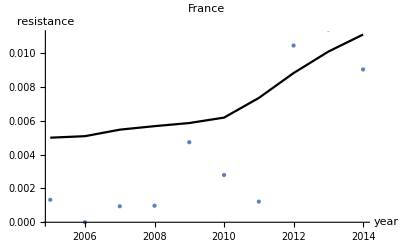

```mathematica
plot1=ListLinePlot[ModelFit, PlotStyle-> {Black},AxesLabel->{year,resistance},PlotLabel-> France, PlotRange-> All];
plot2=ListPlot[{Res}, PlotStyle-> PointSize[Large],PlotRange-> All];
Show[plot1,plot2]
```

```mathematica
Least Squares (Preliminary)
```

```mathematica
Lik[t_,r0_,a_]:=(r[t,r0,a]-RData[[t]])^2;
(* Calculate the sum of the square difference between model output and resistance data (Rdata) then minimize the likelihood to find parameters a and r0 *)
```

```mathematica
t=Range[1,10];
```

```mathematica
Liksum[r0_,a_]:=Total[Lik[t,r0,a]];
```

```mathematica
{max,{LSr0,LSa}}=FindMinimum[{Liksum[r0,a],.005≤ r0≤1},{r0,a}]
```

```mathematica
{0.00010637967427813011,{r0->0.005222197927580822,a->6.473462825187571}}
```

```mathematica
LSModelFit=Transpose@{Years,r[t,LSr0[[2]],LSa[[2]]]};
```

Graphical demonstration of the minimum (least squares):

```mathematica
Plot3D[Liksum[r0,a],{r0,0.004,0.0065},{a,3,10}]
```

-Graphics3D-

Values for r0 are plotted along the x-axis (bottom), likelihood is quantified along the z-axis (left side), and amount of selection imposed per unit of consumption is plotted along the y-axis (top).

The coefficient conveying the amount of selection imposed per unit of consumption (here, a = 6.5) can then be used in our evoutionary model to project future carbapenem resistance in response to any future scenario of carbapenem consumption. With future levels of carbapenem resistance in a given scenario in hand, we can apply methods of cost-effectiveness in the face of future discounting to quantify appropriate policies of carbapenem sparing.

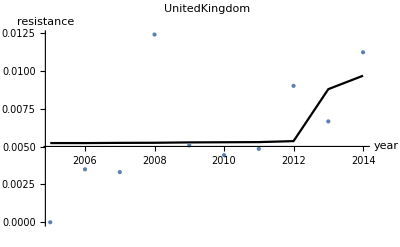

```mathematica
plot1=ListLinePlot[LSModelFit, PlotStyle-> {Black},AxesLabel->{year,resistance},PlotLabel-> UnitedKingdom, PlotRange-> All];
plot2=ListPlot[{Res}, PlotStyle-> PointSize[Large],PlotRange-> All];
Show[plot1,plot2,PlotRange-> All]
```